# Gross-Pitaevskii Equation

```mathematica
vMap=ResourceFunction["ViridisColor"];
```

```mathematica
L=50;
σ=L/5;
```

```mathematica
eqψ = I D[ψ[x,t],t]==(-1/2) D[ψ[x,t],{x,2}]+V ψ[x,t]-Abs[ψ[x,t]]^2 ψ[x,t]
```

ⅈ ψ^(0,1)[x,t]==V ψ[x,t]-Abs[ψ[x,t]]^2 ψ[x,t]-1/2 ψ^(2,0)[x,t]

```mathematica
ψ0=Exp[-(x^2/(2 σ^2))];
```

```mathematica
gpe={eqψ,ψ[x,0]==ψ0,ψ[-L,t]==ψ[L,t]}/.V->(x^2/2);
```

```mathematica
sol=NDSolveValue[gpe,ψ,{x,-L,L},{t,0,1}]
```

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 10.4105 at t = 1. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

InterpolatingFunction[…]

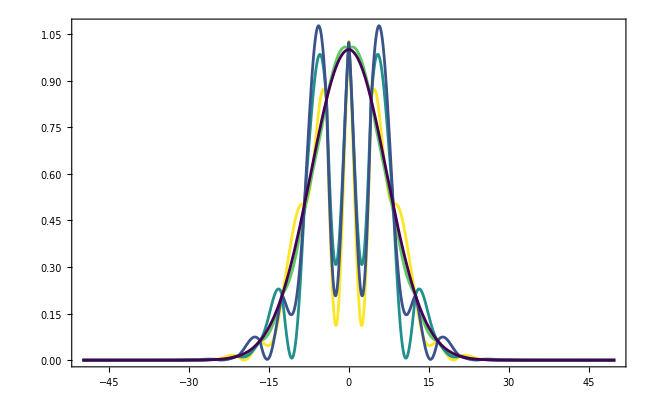

```mathematica
Show[Reverse[Table[Plot[Abs[sol[x,t]]^2,{x,-L,L}, PlotRange->All, Frame->True, PlotStyle->vMap[t]],{t,0,1,0.25}]]]
```

```mathematica
Plot3D[Abs[sol[x,t]]^2,{x,-L,L},{t,0,1}, PlotRange->All, ColorFunction->(vMap[#]&)]
```

-Graphics3D-

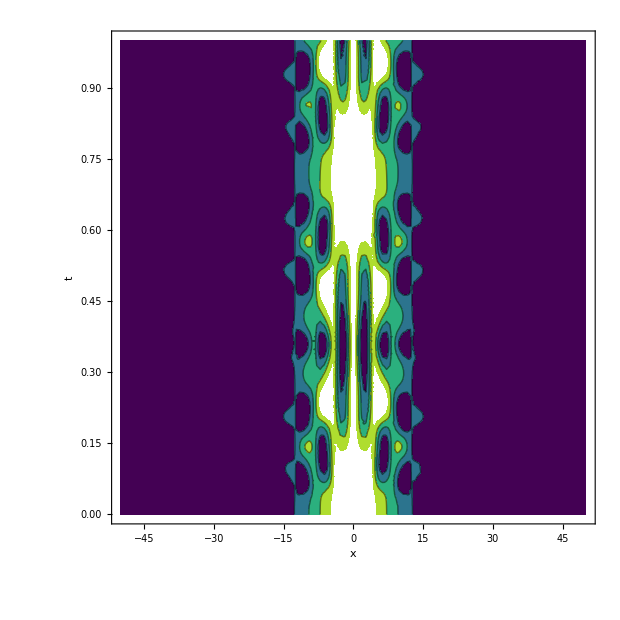

```mathematica
ContourPlot[Abs[sol[x,t]]^2,{x,-L,L}, {t,0,1}, ColorFunction->(vMap[#]&), FrameLabel->{"x", "t"}]
```

```mathematica
animation=Manipulate[Plot[Abs[sol[x,t]]^2,{x,-L,L}, Frame->True,FrameLabel->{"x", "|ψ|^2"}, PlotRange->All, PlotStyle->vMap[0.6], PlotLabel->"Gross-Pitaevskii Evolution"],{t,0,1}]
```

```mathematica
Export["animation.mp4", animation]
```

animation.mp4